```mathematica
tf = 10.0; L = 100.0;
```

```mathematica
μ0= -6.0; σ0=1.0;

ψ0[x_] = Exp[-(x-μ0)^2/ σ0^2 + 2ⅈ x ];
```

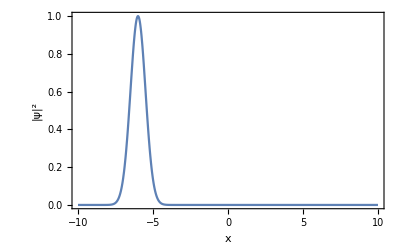
-Graphics-|ψ(0,x)|^2 vs x

```mathematica
Row[{Plot[Abs[ψ0[x]]^2, {x, -0.1L, 0.1L}, PlotRange->All,Frame->True,
FrameLabel->{"x","|ψ|^2"}, FrameTicks->None,ImageSize->{400}],
Spacer[40], "|ψ(0,x)|^2 vs x"}]
```

```mathematica
vL=1; (*barruer spatial size*)
v[x_]=6Exp[-x^2] (*Heaviside[x+vL] HeavisideTheta[vL-x]*);
```

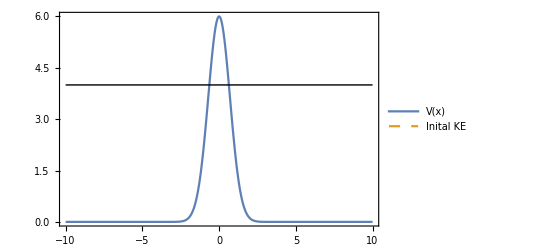

```mathematica
Plot[{v[x], Style[4,Dashed]}, {x, -0.1L, 0.1L}, PlotRange-> All,
Exclusions->None, PlotLegends->{"V(x)","Inital KE"}, Frame->True,
FrameTicks->None]
```

```mathematica
eqns = {ⅈ D[u[t,x],t] == -0.5 D[u[t,x],x,x] + v[x]u[t,x],u[0,x]==ψ0[x],
u[t,L]==0, u[t,-L]==0};
```

```mathematica
expandedeqns =
Flatten[
ComplexExpand[
ReIm[eqns/.{u[x_,t]->uR[x,t]+ⅈ uI[x,t],
Derivative[y__][u][x_,t_]->
Derivative[y][uR][x,t] + ⅈ Derivative[y][uI][x,t]}
]]];
```

```mathematica
sol = NDSolve[Evaluate[expandedeqns],{uR,uI},{t,0,tf},
{x,-L,L}, AccuracyGoal->5]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {-uI^(1,0)[t,x]==6 ⅇ^(-x^2) u[t,x]-0.5 uR^(0,2)[t,x],uR^(1,0)[t,x]==-0.5 uI^(0,2)[t,x],u[0,x]==ⅇ^(-1. (6.+x)^2) Cos[0.+2 x],0==ⅇ^(-1. (6.+x)^2) Sin[0.+2 x],u[t,100.]==0,True,u[t,-100.]==0,True}.

NDSolve[{-uI^(1,0)[t,x]==6 ⅇ^(-x^2) u[t,x]-0.5 uR^(0,2)[t,x],uR^(1,0)[t,x]==-0.5 uI^(0,2)[t,x],u[0,x]==ⅇ^(-1. (6.+x)^2) Cos[0.+2 x],0==ⅇ^(-1. (6.+x)^2) Sin[0.+2 x],u[t,100.]==0,True,u[t,-100.]==0,True},{uR,uI},{t,0,10.},{x,-100.,100.},AccuracyGoal→5]

```mathematica
ρ[t_,x_] = (uI[t,x]^2+uR[t,x]^2)/.sol
```

```mathematica
Manipulate[
Plot[{ρ[t,x]} {x,-0.1L, 0.1L}, PlotRange -> {0, ρMax}, Ticks->None,
GridLines->{{-vL,vL},None}, GridLinesStyle->Directive[Orange, Dashed],
AxesLabel->{"x","|ψ(t,x)|^2"}],
{{t,0,Row[{Spacer[50],"time"}]}, 0, tf},
{{ρMax, 1, "Max.ρ"},1,.1,VerticalSlider}, ControlPlacement->{Top,Left}]
```